```mathematica
data={0,1,18, 31,6};
```

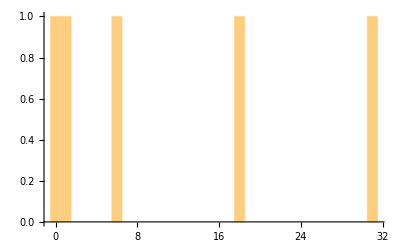

```mathematica
Histogram[data,Max[data]]
```

```mathematica
histogramList=HistogramList[data,Max[data]][[2]]
```

{1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
probabilities=histogramList/Length[data]
```

{1/5,1/5,0,0,0,0,1/5,0,0,0,0,0,0,0,0,0,0,0,1/5,0,0,0,0,0,0,0,0,0,0,0,0,1/5}

```mathematica
G[z_]:=Module[{},
sum=0;
For[i=1,i<=Length[histogramList],i++,
sum=sum+(Power[z,i-1])*probabilities[[i]]];
sum]
G[1.0]
```

1.

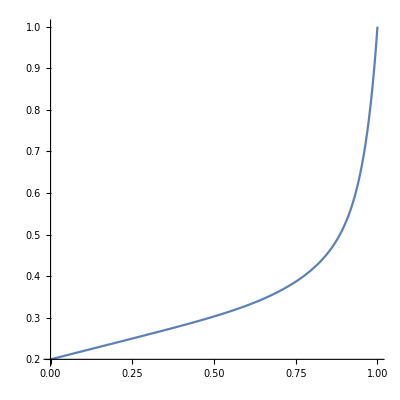

```mathematica
Plot[G[z],{z,0,1},AspectRatio->1,PlotRange->All]
```